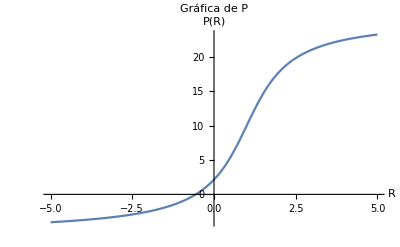

```mathematica
P[R_,PRef_,α_,β_]:=PRef*(1+α*ArcTan[β*(R-1)])
Plot[P[R,10,1,1],{R,-5,5},PlotLabel->"Gráfica de P",AxesLabel->{"R","P(R)"}]
```

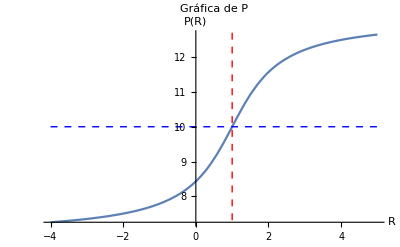

```mathematica
Plot[P[R,10,0.2,1],{R,-4,5},PlotLabel->"Gráfica de P",AxesLabel->{"R","P(R)"},Epilog->{
Red,Dashed,Line[{{1,-2},{1,20}}],(*Línea vertical en R=1*)
Blue,Dashed,Line[{{-4,10},{5,10}}] (*Línea horizontal en PRef*)
}]
```

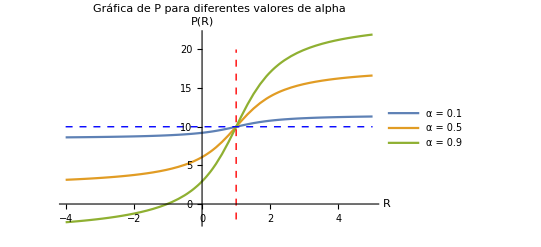

```mathematica
Plot[{P[R,10,0.1,1],P[R,10,0.5,1],P[R,10,0.9,1]},{R,-4,5},PlotLabel->"Gráfica de P para diferentes valores de alpha",PlotLegends->{"α = 0.1","α = 0.5","α = 0.9"},AxesLabel->{"R","P(R)"},Epilog->{Red,Dashed,Line[{{1,-2},{1,20}}],(*Línea vertical en R=1*)Blue,Dashed,Line[{{-4,10},{5,10}}] (*Línea horizontal en PRef=10*)}]
```